NODO INESTABLE

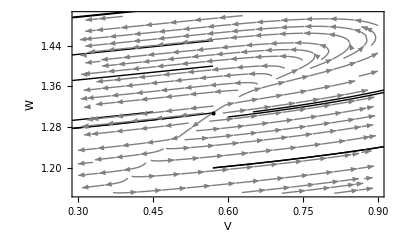

```mathematica
a = 1; b = 1.2; T = 0.8; phi = 0.08;
f[{V_, W_}] := {V - V^3/3 - W + T, phi (V + a - b W)};
y0Val = {{0.5696, 1.3080}, {0.6, 1.3}, {0.5, 1.3}, {0.57, 1.2}, {0.57, 1.4}, {0.65, 1.31}, {0.45, 1.31}, {0.5696, 1.45}, {0.5696, 1.2}};
VRango = {0.3, 0.9}; WRango = {1.15, 1.5};

sol = Table[NDSolve[{
      V'[t] == f[{V[t], W[t]}][[1]], W'[t] == f[{V[t], W[t]}][[2]],
      V[0] == y0Val[[i, 1]], W[0] == y0Val[[i, 2]]}, {V, W}, {t, 0, 1000}], {i, 1, Length[y0Val]}];

tray = Table[ParametricPlot[Evaluate[{V[t], W[t]} /. sol[[i]]], {t, 0, 1000}, PlotStyle -> {Black, Thick}], {i, 1, Length[y0Val]}];

campo = StreamPlot[f[{V, W}], {V, VRango[[1]], VRango[[2]]}, {W, WRango[[1]], WRango[[2]]}, StreamColorFunction -> None, StreamStyle -> Directive[Gray]];

punto = Graphics[{Black, PointSize[Large], Point[{0.5696, 1.3080}]}];

Show[tray, campo, punto, PlotRange -> {VRango, WRango},  Frame -> True, FrameLabel -> {Style[ToExpression["V", TeXForm, HoldForm]], Style[ToExpression["W", TeXForm, HoldForm]]}]
```

NODO ESTABLE

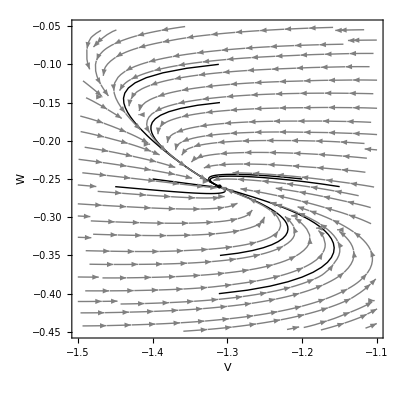

```mathematica
a = 1; b = 1.2; T = 0.3; phi = 0.08;
f[{V_, W_}] := {V - V^3/3 - W + T, phi (V + a - b W)};
y0Val = {{-1.3115, -0.2596}, {-1.4, -0.25}, {-1.2, -0.25}, {-1.31, -0.15}, {-1.31, -0.35}, {-1.45, -0.26}, {-1.15, -0.26}, {-1.3115, -0.4}, {-1.3115, -0.1}};
VRango = {-1.5, -1.1}; WRango = {-0.45, -0.05};

sol = Table[NDSolve[{
      V'[t] == f[{V[t], W[t]}][[1]], W'[t] == f[{V[t], W[t]}][[2]],
      V[0] == y0Val[[i, 1]], W[0] == y0Val[[i, 2]]}, {V, W}, {t, 0, 1000}], {i, 1, Length[y0Val]}];

tray = Table[ParametricPlot[Evaluate[{V[t], W[t]} /. sol[[i]]], {t, 0, 1000}, PlotStyle -> {Black, Thick}], {i, 1, Length[y0Val]}];

campo = StreamPlot[f[{V, W}], {V, VRango[[1]], VRango[[2]]}, {W, WRango[[1]], WRango[[2]]}, StreamColorFunction -> None, StreamStyle -> Directive[Gray]];

punto = Graphics[{Black, PointSize[Large], Point[{-1.3115, -0.2596}]}];

Show[tray, campo, punto, PlotRange -> {VRango, WRango}, Axes -> False,  Frame -> True, FrameLabel -> {Style[ToExpression["V", TeXForm, HoldForm]], Style[ToExpression["W", TeXForm, HoldForm]]}]
```

FOCO INESTABLE

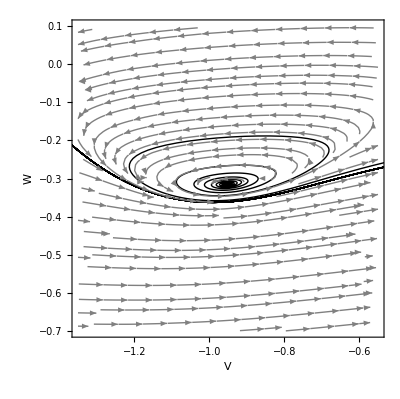

```mathematica
a = 0.7; b = 0.8; T = 0.35; phi = 0.08;
f[{V_, W_}] := {V - V^3/3 - W + T, phi (V + a - b W)};
y0Val = {{-0.9515, -0.3143}};
VRango = {-1.35, -0.55}; WRango = {-0.7, 0.1};

sol = Table[NDSolve[{
      V'[t] == f[{V[t], W[t]}][[1]], W'[t] == f[{V[t], W[t]}][[2]],
      V[0] == y0Val[[i, 1]], W[0] == y0Val[[i, 2]]}, {V, W}, {t, 0, 1000}], {i, 1, Length[y0Val]}];

tray = Table[ParametricPlot[Evaluate[{V[t], W[t]} /. sol[[i]]], {t, 0, 1000}, PlotStyle -> {Black, Thick}], {i, 1, Length[y0Val]}];

campo = StreamPlot[f[{V, W}], {V, VRango[[1]], VRango[[2]]}, {W, WRango[[1]], WRango[[2]]}, StreamColorFunction -> None, StreamStyle -> Directive[Gray]];

punto = Graphics[{Black, PointSize[Large], Point[{-0.9515, -0.3143}]}];

Show[tray, campo, punto, PlotRange -> {VRango, WRango}, Axes -> False, Frame -> True, FrameLabel -> {Style[ToExpression["V", TeXForm, HoldForm]], Style[ToExpression["W", TeXForm, HoldForm]]}]
```

FOCO ESTABLE

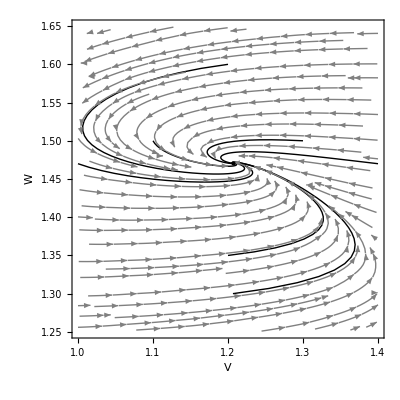

```mathematica
a = 1; b = 1.5; T = 0.85; phi = 0.08;
f[{V_, W_}] := {V - V^3/3 - W + T, phi (V + a - b W)};
y0Val = {{1.2066, 1.4711}, {1.3, 1.5}, {1.1, 1.5}, {1.2, 1.6}, {1.2, 1.35}, {1.4, 1.47}, {1.0, 1.47}, {1.2066, 1.3}};
VRango = {1, 1.4}; WRango = {1.25, 1.65};

sol = Table[NDSolve[{
      V'[t] == f[{V[t], W[t]}][[1]], W'[t] == f[{V[t], W[t]}][[2]],
      V[0] == y0Val[[i, 1]], W[0] == y0Val[[i, 2]]}, {V, W}, {t, 0, 1000}], {i, 1, Length[y0Val]}];

tray = Table[ParametricPlot[Evaluate[{V[t], W[t]} /. sol[[i]]], {t, 0, 1000}, PlotStyle -> {Black, Thick}], {i, 1, Length[y0Val]}];

campo = StreamPlot[f[{V, W}], {V, VRango[[1]], VRango[[2]]}, {W, WRango[[1]], WRango[[2]]}, StreamColorFunction -> None, StreamStyle -> Directive[Gray]];

punto = Graphics[{Black, PointSize[Large], Point[{1.2066,  1.4711}]}];

Show[tray, campo, punto, PlotRange -> {VRango, WRango}, Axes -> False, Frame -> True, FrameLabel -> {Style[ToExpression["V", TeXForm, HoldForm]], Style[ToExpression["W", TeXForm, HoldForm]]}]
```

CENTRO

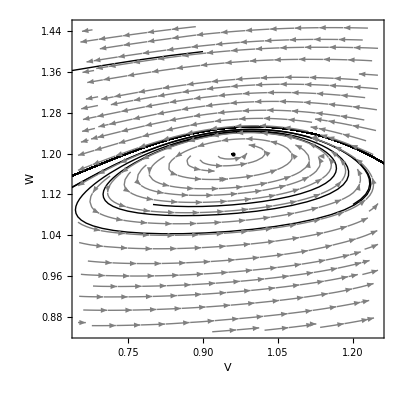

```mathematica
a = 0; b = 0.8; T = 3249/6085; phi = 0.1;
f[{V_, W_}] := {V - V^3/3 - W + T, phi (V + a - b W)};
y0Val = {{0.9592, 1.1990}, {0.8, 1.1}, {0.9, 1.4}, {1.2, 1.1}};
VRango = {0.65, 1.25}; WRango = {0.85, 1.45};

sol = Table[NDSolve[{
      V'[t] == f[{V[t], W[t]}][[1]], W'[t] == f[{V[t], W[t]}][[2]],
      V[0] == y0Val[[i, 1]], W[0] == y0Val[[i, 2]]}, {V, W}, {t, 0, 1000}], {i, 1, Length[y0Val]}];

tray = Table[ParametricPlot[Evaluate[{V[t], W[t]} /. sol[[i]]], {t, 0, 1000}, PlotStyle -> {Black, Thick}], {i, 1, Length[y0Val]}];

campo = StreamPlot[f[{V, W}], {V, VRango[[1]], VRango[[2]]}, {W, WRango[[1]], WRango[[2]]}, StreamColorFunction -> None, StreamStyle -> Directive[Gray]];

punto = Graphics[{Black, PointSize[Large], Point[{0.9592, 1.1990}]}];

Show[tray, campo, punto, PlotRange -> {VRango, WRango}, Axes -> False, Frame -> True, FrameLabel -> {Style[ToExpression["V", TeXForm, HoldForm]], Style[ToExpression["W", TeXForm, HoldForm]]}]
```

PUNTO DE SILLA

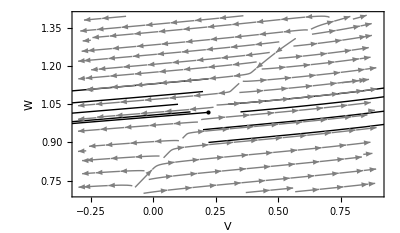

```mathematica
a = 1; b = 1.2; T = 0.8; phi = 0.08;
f[{V_, W_}] := {V - V^3/3 - W + T, phi (V + a - b W)};
y0Val = {{0.2218, 1.0182}, {0.3, 1.05}, {0.1, 1.05}, {0.2, 0.95}, {0.2, 1.1}, {0.35, 1.02}, {0.15, 1.02}, {0.2218, 1.15}, {0.2218, 0.9}};
VRango = {-0.3, 0.9}; WRango = {0.7, 1.4};

sol = Table[NDSolve[{
      V'[t] == f[{V[t], W[t]}][[1]], W'[t] == f[{V[t], W[t]}][[2]],
      V[0] == y0Val[[i, 1]], W[0] == y0Val[[i, 2]]}, {V, W}, {t, 0, 1000}], {i, 1, Length[y0Val]}];

tray = Table[ParametricPlot[Evaluate[{V[t], W[t]} /. sol[[i]]], {t, 0, 1000}, PlotStyle -> {Black, Thick}], {i, 1, Length[y0Val]}];

campo = StreamPlot[f[{V, W}], {V, VRango[[1]], VRango[[2]]}, {W, WRango[[1]], WRango[[2]]}, StreamColorFunction -> None, StreamStyle -> Directive[Gray]];

punto = Graphics[{Black, PointSize[Large], Point[{0.2218, 1.0182}]}];

Show[tray, campo, punto, PlotRange -> {VRango, WRango}, Axes -> False, Frame -> True, FrameLabel -> {Style[ToExpression["V", TeXForm, HoldForm]], Style[ToExpression["W", TeXForm, HoldForm]]}]
```